```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

## Setup

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->jStyle["FontFamily"],FontSize->n};
```

## Decussate etc

```mathematica
leafRose = Import["Data\\LeafMesh.mx"];
l1 = TransformedRegion[leafRose,ReflectionTransform[{0,1,0}]@* TranslationTransform[{-2604,-1814,0}]];
```

```mathematica
l2 =TransformedRegion[l1,ReflectionTransform[{1,0,0}]@*ReflectionTransform[{0,1,0}]];
```

```mathematica
l12 = RegionUnion[l1,l2];
```

```mathematica
l12
```

-Graphics3D-

```mathematica
l123= RegionUnion[l1
,TransformedRegion[l1,RotationTransform[ 120 Degree,{0,0,1}]]
,TransformedRegion[l1,RotationTransform[ 240 Degree,{0,0,1}]]
];

gLeaf[{height_,rotation_}] := MeshPrimitives[#,2]& @TransformedRegion[l1,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];

gLeafPair[{height_,rotation_}] := MeshPrimitives[#,2]& @TransformedRegion[l12,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];

gWhorl[{height_,rotation_}] := MeshPrimitives[#,2]& @
TransformedRegion[l123,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];
```

```mathematica
spiral:= Module[{pairTable},
pairTable= Table[gLeaf[ {100 *n,20  Degree+GoldenAngle * n}],{n,0,5}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
alternateDistichous:= Module[{pairTable},
pairTable= Table[gLeaf[ {100 *n,-20  Degree+180 Degree * n}],{n,0,5}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
oppositeDistichous := Module[{pairTable},
pairTable= Table[gLeafPair[ {100+200 *n,-20 Degree}],{n,0,2}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
```

```mathematica
m12= mLeafPair[ {0,0}]
```

```mathematica
Take[MeshPrimitives[m12,2],2]
```

{Polygon[…],Polygon[…]}

```mathematica
Graphics3D[MeshPrimitives[m12,2]]
```

-Graphics3D-

```mathematica
mLeafPair[{height_,rotation_}] := TransformedRegion[l12,RotationTransform[rotation,{0,0,1}]@*TranslationTransform[{0,0,height}]];
```

```mathematica
pairTable= Table[gLeafPair[ {100+200 *n,-20 Degree}],{n,0,2}]
```

$Aborted

```mathematica
oppositeDecussate := Module[{pairTable},
pairTable= Table[gLeafPair[ {100+200 *n,-20 + n  90Degree}],{n,0,2}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
whorled := Module[{pairTable},
pairTable= Table[gWhorl[ {100+200 *n,-20 + n  90Degree}],{n,0,2}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,520}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
decussate := Module[{pairTable},
pairTable= Table[gLeafPair[ {100 *n,90 Degree * n}],{n,0,5}];
Graphics3D[{
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[Black],Cylinder[{{0,0,0},{0,0,500}},2]}
,
{FaceForm[jStyle["CylinderColour3D"]],EdgeForm[None],pairTable}
}]
];
```

```mathematica
Ch3Types := Module[{},
 types ={
<|"label"->"Spiral","graphics"->spiral,"jugacy"->1,
"lattice"->spiralLattice,"class"-> "(0,1)"|>
,<|"label"->"Alternate\ndistichous","graphics"->alternateDistichous,"jugacy"->1,
"lattice"->alternateDistichousLattice,"class"-> "(0,1=1)"|>
,<|"label"->"Opposite\ndistichous","graphics"->oppositeDistichous,"jugacy"->2,
"lattice"->oppositeDistichousLattice,"class"-> "2x(0,1,1)"|>
,<|"label"->"Decussate","graphics"->oppositeDecussate,"jugacy"->2,
"lattice"->oppositeDecussateLattice,"class"-> "2x(0,1=1)"|>
,<|"label"->"Whorled","graphics"->whorled,"jugacy"->3,
"lattice"->whorledLattice,"class"-> "3x(0,1,1)"|>
};
boxsize= 50;raster[g_] := Rasterize[#,ImageResolution->300,ImageSize->72]& @ Show[Graphics3D[{Opacity[0.],EdgeForm[None],Cuboid[{-boxsize,-boxsize,0},{boxsize,boxsize,520}]}],g,Boxed->False];

rtypes = Map[Append[#,"raster"->raster[#["graphics"]]]&,types];
data = Map[  {Item[#["raster"],ItemSize->Automatic]
,Item[Style[#["label"],jFont[12]],ItemSize->All]
,("J="<> ToString[#["jugacy"]] )
, Style[#["class"],jFont[12]]
, #["lattice"]
}&,rtypes];
Grid[Transpose[data]]
];
```

```mathematica
spiralLattice := Module[{},lattice= latticeCreateDH[{1/GoldenRatio^2,1},{-0.1,5.1}];
jpt[m_] := latticePoint[lattice,m];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.06],White,Point[ latticePoints[ lattice]],
{White,Point[latticePoint[lattice,1]-{1,0}],Point[latticePoint[lattice,3]+{1,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]}]}
},jFont[Scaled[0.03]]]
}
},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
alternateDistichousLattice := Module[{},lattice= latticeCreateDH[{1/2,1},{-0.1,5.1}];
jpt[m_] := latticePoint[lattice,m];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.06],White,Point[ latticePoints[ lattice]],
{White,Point[latticePoint[lattice,1]-{1,0}],Point[latticePoint[lattice,3]+{1,0}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]}]},
{Thick,jParastichyColour[1],Arrow[{jpt[0],jpt[1]-{1,0}}]}
},jFont[Scaled[0.03]]]
}
},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
decussateLattice := Module[{},
lattice= latticeCreateDH[{1/2,1},{-0.1,5.1}];
lpts=Point[{{-1/8,0},{3/8,0},{-3/8,2},{1/8,2},{-1/8,4},{3/8,4}}];
g = Graphics[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{PointSize[0.06],White,lpts}
,{Thick,jParastichyColour[1],Arrow[{{-1/8,0},{-3/8,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{-1/8,0},{1/8,2}}]}

},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
oppositeDistichousLattice := Module[{},
lpts=Point[{{-1/8,0},{3/8,0},{-1/8,2},{3/8,2},{-1/8,4},{3/8,4}}];
g = Graphics[
{
{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,{PointSize[0.06],White,lpts}
,{Thick,jParastichyColour[1],Arrow[{{-1/8,0},{-1/8,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{-1/8,0},{3/8,2}}]}

},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
oppositeDecussateLattice=oppositeDistichousLattice;
```

```mathematica
whorledLattice := Module[{},lattice= latticeCreateDH[{1/2,1},{-0.1,5.1}];
lpts=Point[{{-2/6,0},{0,0},{2/6,0},{-1/6,2},{1/6,2},{3/6,2},{-2/6,4},{0,4},{2/6,4}}];
g = Graphics[
{{Style[
{{jStyle["CylinderColour"],latticeGraphicsCylinder[lattice]}
,PointSize[0.06],White,lpts
,{Thick,jParastichyColour[1],Arrow[{{0,0},{-1/6,2}}]}
,{Thick,jParastichyColour[2],Arrow[{{0,0},{1/6,2}}]}
},jFont[Scaled[0.03]]]
}
},
PlotRange->{{-1/2,1/2},{-0.1,5.1}},Axes->False,AspectRatio->Automatic
];
g
];
```

```mathematica
Txb0401LeafTypes=Ch3Types;
```

```mathematica
txbExport[Txb0401LeafTypes];
```

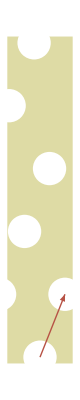
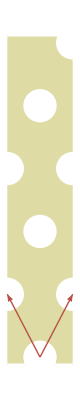
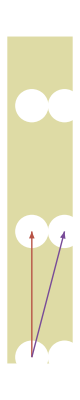
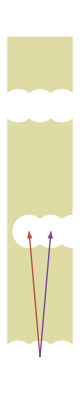
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Spiral | Alternate
distichous | Opposite
distichous | Decussate | Whorled
J=1 | J=1 | J=2 | J=2 | J=3
(0,1) | (0,1=1) | 2x(0,1,1) | 2x(0,1=1) | 3x(0,1,1)
-Graphics- | -Graphics- | -Graphics- | oppositeDecussateLattice | -Graphics-

```mathematica
Txb0401LeafTypes
```